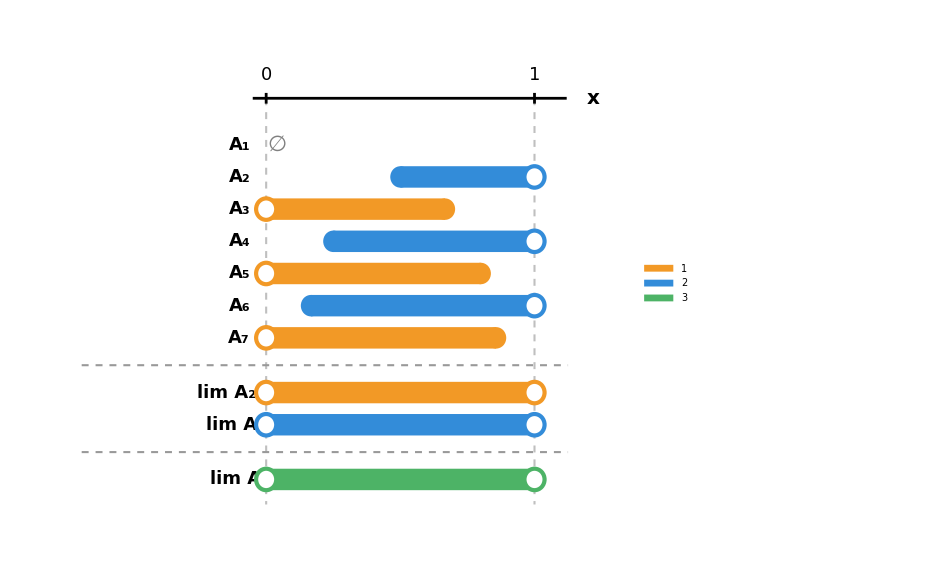

```mathematica
ClearAll[esc, sep, h, barra, puntoCerrado, puntoAbierto, etiquetaFila];

esc = 8;      (* factor de escala horizontal *)
sep = 0.9;    (* separación vertical entre filas *)
h = 0.3;      (* semialtura de cada barra *)
nMax = 7;

colorImpar = RGBColor[0.95, 0.6, 0.15];
colorPar = RGBColor[0.2, 0.55, 0.85];
colorLim = RGBColor[0.3, 0.7, 0.4];

barra[l_, r_, y_, col_] := {col, Rectangle[{esc l, y - h}, {esc r, y + h}]};
puntoCerrado[x_, y_, col_] := {col, Disk[{esc x, y}, h]};
puntoAbierto[x_, y_, col_] := {White, Disk[{esc x, y}, h],
   col, AbsoluteThickness[3], Circle[{esc x, y}, h]};
etiquetaFila[txt_, y_] := Text[Style[txt, 18, Bold], {-0.8, y}, {1, 0}];

(* ---------- filas A_n ---------- *)
filaA[n_] := Module[{y = -(n - 1) sep},
   If[OddQ[n],
    If[n == 1,
     Text[Style["∅", 22, GrayLevel[0.5]], {esc 0.04, y}],
     {barra[0, 1 - 1/n, y, colorImpar], puntoAbierto[0, y, colorImpar],
      puntoCerrado[1 - 1/n, y, colorImpar]}],
    {barra[1/n, 1, y, colorPar], puntoCerrado[1/n, y, colorPar],
     puntoAbierto[1, y, colorPar]}]
   ];

filasA = Table[filaA[n], {n, 1, nMax}];
etiquetasA = Table[etiquetaFila[Subscript["A", n], -(n - 1) sep], {n, 1, nMax}];

(* ---------- posiciones de las filas resumen ---------- *)
yUlt = -(nMax - 1) sep;
ySep1 = yUlt - 0.85 sep;
yLimImp = ySep1 - 0.85 sep;
yLimPar = yLimImp - sep;
ySep2 = yLimPar - 0.85 sep;
yLim = ySep2 - 0.85 sep;

limImpar = {barra[0, 1, yLimImp, colorImpar], puntoAbierto[0, yLimImp, colorImpar],
   puntoAbierto[1, yLimImp, colorImpar]};
limPar = {barra[0, 1, yLimPar, colorPar], puntoAbierto[0, yLimPar, colorPar],
   puntoAbierto[1, yLimPar, colorPar]};
limTotal = {barra[0, 1, yLim, colorLim], puntoAbierto[0, yLim, colorLim],
   puntoAbierto[1, yLim, colorLim]};

etiquetasLim = {
   etiquetaFila[Row[{"lim ", Subscript["A", "2n-1"]}], yLimImp],
   etiquetaFila[Row[{"lim ", Subscript["A", "2n"]}], yLimPar],
   etiquetaFila[Row[{"lim ", Subscript["A", "n"]}], yLim]};

separadores = {GrayLevel[0.6], Dashed, AbsoluteThickness[1.5],
   Line[{{-5.5, ySep1}, {esc + 1, ySep1}}],
   Line[{{-5.5, ySep2}, {esc + 1, ySep2}}]};

(* ---------- eje real y guías en 0 y 1 ---------- *)
yEje = 1.3;
guias = {GrayLevel[0.75], Dashed, AbsoluteThickness[1.5],
   Line[{{0, yEje}, {0, yLim - 0.7}}], Line[{{esc, yEje}, {esc, yLim - 0.7}}]};

ejeReal = {Black, AbsoluteThickness[2],
   Line[{{-0.05 esc, yEje}, {1.12 esc, yEje}}],
   Line[{{0, yEje - 0.15}, {0, yEje + 0.15}}],
   Line[{{esc, yEje - 0.15}, {esc, yEje + 0.15}}],
   Text[Style["0", 18], {0, yEje + 0.65}],
   Text[Style["1", 18], {esc, yEje + 0.65}],
   Text[Style["x", 20, Bold], {1.12 esc + 0.8, yEje}]};

grafico = Graphics[
   {guias, ejeReal, filasA, etiquetasA, separadores, limImpar, limPar, limTotal, etiquetasLim},
   PlotRange -> {{-5.5, esc + 2.5}, {yLim - 1, yEje + 1.3}}, ImageSize -> 700];

T4P1a = Legended[grafico,
   SwatchLegend[{colorImpar, colorPar, colorLim},
    {"Aₙ, n impar", "Aₙ, n par", "lim Aₙ"},
    LabelStyle -> Directive[FontSize -> 16], LegendMarkerSize -> 20]];

T4P1a
```

```mathematica
Export[CloudObject["T4_P1_a.png"], T4P1a, "PNG", Background -> None, ImageResolution -> 300, ImageSize -> 700]
```

CloudObject[https://www.wolframcloud.com/obj/jesusparejop/T4_P1_a.png]

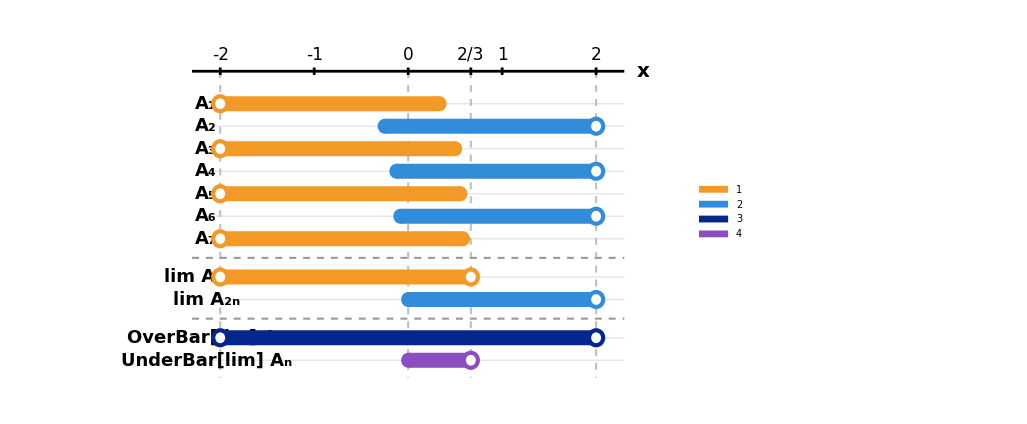

```mathematica
ClearAll[esc, sep, h, barra, puntoCerrado, puntoAbierto, etiquetaFila];

esc = 4;      (* factor de escala horizontal *)
sep = 0.9;
h = 0.3;
nMax = 7;

colorImpar = RGBColor[0.95, 0.6, 0.15];
colorPar = RGBColor[0.2, 0.55, 0.85];
colorLimsup = RGBColor[0.02, 0.15, 0.55];
colorLiminf = RGBColor[0.55, 0.3, 0.75];

barra[l_, r_, y_, col_] := {col, Rectangle[{esc l, y - h}, {esc r, y + h}]};
puntoCerrado[x_, y_, col_] := {col, Disk[{esc x, y}, h]};
puntoAbierto[x_, y_, col_] := {White, Disk[{esc x, y}, h],
   col, AbsoluteThickness[3], Circle[{esc x, y}, h]};
etiquetaFila[txt_, y_] := Text[Style[txt, 18, Bold], {-2.15 esc, y}, {1, 0}];

(* extremos de los términos: n impar -> (-2, derImpar], n par -> [izqPar, 2) *)
derImpar[n_] := With[{m = (n + 1)/2}, (4 m - 2)/(6 m)];
izqPar[n_] := -1/(2 n);

(* ---------- filas A_n ---------- *)
filaA[n_] := Module[{y = -(n - 1) sep},
   If[OddQ[n],
    {barra[-2, derImpar[n], y, colorImpar], puntoAbierto[-2, y, colorImpar],
     puntoCerrado[derImpar[n], y, colorImpar]},
    {barra[izqPar[n], 2, y, colorPar], puntoCerrado[izqPar[n], y, colorPar],
     puntoAbierto[2, y, colorPar]}]
   ];

filasA = Table[filaA[n], {n, 1, nMax}];
etiquetasA = Table[etiquetaFila[Subscript["A", n], -(n - 1) sep], {n, 1, nMax}];

(* ---------- posiciones de las filas resumen ---------- *)
yUlt = -(nMax - 1) sep;
ySep1 = yUlt - 0.85 sep;
yLimImp = ySep1 - 0.85 sep;
yLimPar = yLimImp - sep;
ySep2 = yLimPar - 0.85 sep;
yLimsup = ySep2 - 0.85 sep;
yLiminf = yLimsup - sep;

(* límites de las subcadenas: (-2, 2/3) y [0, 2) *)
limImpar = {barra[-2, 2/3, yLimImp, colorImpar], puntoAbierto[-2, yLimImp, colorImpar],
   puntoAbierto[2/3, yLimImp, colorImpar]};
limPar = {barra[0, 2, yLimPar, colorPar], puntoCerrado[0, yLimPar, colorPar],
   puntoAbierto[2, yLimPar, colorPar]};

(* limsup = (-2, 2) y liminf = [0, 2/3) *)
limsup = {barra[-2, 2, yLimsup, colorLimsup], puntoAbierto[-2, yLimsup, colorLimsup],
   puntoAbierto[2, yLimsup, colorLimsup]};
liminf = {barra[0, 2/3, yLiminf, colorLiminf], puntoCerrado[0, yLiminf, colorLiminf],
   puntoAbierto[2/3, yLiminf, colorLiminf]};

etiquetasLim = {
   etiquetaFila[Row[{"lim ", Subscript["A", "2n-1"]}], yLimImp],
   etiquetaFila[Row[{"lim ", Subscript["A", "2n"]}], yLimPar],
   etiquetaFila[Row[{OverBar["lim"], " ", Subscript["A", "n"]}], yLimsup],
   etiquetaFila[Row[{UnderBar["lim"], " ", Subscript["A", "n"]}], yLiminf]};

(* ---------- líneas tenues de fila, separadores y guías ---------- *)
todasY = Join[Table[-(n - 1) sep, {n, 1, nMax}], {yLimImp, yLimPar, yLimsup, yLiminf}];
lineasFila = {GrayLevel[0.9], AbsoluteThickness[1],
   Table[Line[{{-2.1 esc, y}, {2.3 esc, y}}], {y, todasY}]};

separadores = {GrayLevel[0.6], Dashed, AbsoluteThickness[1.5],
   Line[{{-2.3 esc, ySep1}, {2.3 esc, ySep1}}],
   Line[{{-2.3 esc, ySep2}, {2.3 esc, ySep2}}]};

yEje = 1.3;
guias = {GrayLevel[0.75], Dashed, AbsoluteThickness[1.5],
   Table[Line[{{esc k, yEje}, {esc k, yLiminf - 0.7}}], {k, {-2, 0, 2/3, 2}}]};

ejeReal = {Black, AbsoluteThickness[2],
   Line[{{-2.3 esc, yEje}, {2.3 esc, yEje}}],
   Table[Line[{{esc k, yEje - 0.15}, {esc k, yEje + 0.15}}], {k, {-2, -1, 0, 1, 2, 2/3}}],
   Table[Text[Style[k, 17], {esc k, yEje + 0.65}], {k, {-2, -1, 0, 1, 2}}],
   Text[Style["2/3", 17], {esc 2/3, yEje + 0.65}],
   Text[Style["x", 20, Bold], {2.3 esc + 0.8, yEje}]};

grafico = Graphics[
   {lineasFila, guias, ejeReal, filasA, etiquetasA, separadores,
    limImpar, limPar, limsup, liminf, etiquetasLim},
   PlotRange -> {{-2.15 esc - 5, 2.3 esc + 2}, {yLiminf - 1, yEje + 1.3}},
   ImageSize -> 760];

T4P1b = Legended[grafico,
   SwatchLegend[{colorImpar, colorPar, colorLimsup, colorLiminf},
    {"Aₙ, n impar", "Aₙ, n par",
     Row[{OverBar["lim"], " Aₙ"}], Row[{UnderBar["lim"], " Aₙ"}]},
    LabelStyle -> Directive[FontSize -> 16], LegendMarkerSize -> 20]];

T4P1b
```

```mathematica
Export[CloudObject["T1_P1_b.png"], T1P1b, "PNG", Background -> None, ImageResolution -> 300, ImageSize -> 700]
```

CloudObject[https://www.wolframcloud.com/obj/jesusparejop/T4_P1_b.png]

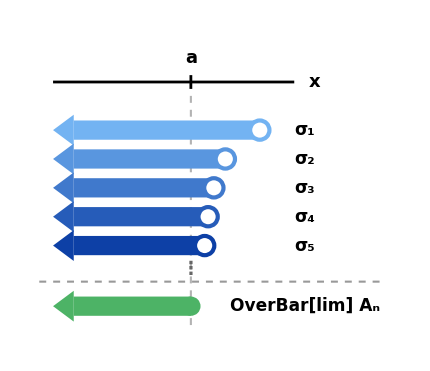
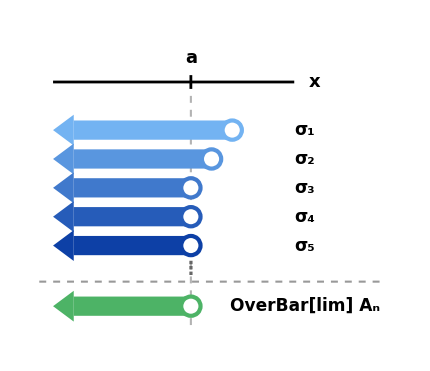
Caso 1
-Graphics-Caso 2
-Graphics-

```mathematica
ClearAll[h, sep, xL, a, colorLim, colorSigma, rayo, puntoAbierto, puntoCerrado, panelCaso];

h = 0.14;      (* semialtura de cada barra *)
sep = 0.42;    (* separación vertical entre filas *)
xL = -0.7;     (* extremo izquierdo de los rayos *)
a = 1;
colorLim = RGBColor[0.3, 0.7, 0.4];

colorSigma[k_, n_] := Blend[{RGBColor[0.45, 0.7, 0.95], RGBColor[0.05, 0.25, 0.65]}, (k - 1)/(n - 1)];

rayo[s_, y_, col_] := {col, Rectangle[{xL, y - h}, {s, y + h}],
   Polygon[{{xL, y + 1.6 h}, {xL, y - 1.6 h}, {xL - 0.3, y}}]};
puntoAbierto[x_, y_, col_] := {White, Disk[{x, y}, h], col, AbsoluteThickness[3], Circle[{x, y}, h]};
puntoCerrado[x_, y_, col_] := {col, Disk[{x, y}, h]};

panelCaso[sVals_List, limCerrado_, titulo_] := Module[
   {n = Length[sVals], yEje = 0.7, yUlt, ySepar, yLim,
    guia, eje, filas, etiquetas, puntos, separador, limite, etiquetaLim},
   yUlt = -(n - 1) sep;
   ySepar = yUlt - 1.25 sep;
   yLim = yUlt - 2.1 sep;

   guia = {GrayLevel[0.7], Dashed, AbsoluteThickness[1.5],
     Line[{{a, yEje}, {a, yLim - 0.35}}]};

   eje = {Black, AbsoluteThickness[2], Line[{{xL - 0.3, yEje}, {2.5, yEje}}],
     Line[{{a, yEje - 0.1}, {a, yEje + 0.1}}],
     Text[Style["a", 18, Bold], {a, yEje + 0.35}],
     Text[Style["x", 18, Bold], {2.8, yEje}]};

   (* filas sigma_k = (-inf, s_k) *)
   filas = Table[
     With[{y = -(k - 1) sep, col = colorSigma[k, n]},
      {rayo[sVals[[k]], y, col], puntoAbierto[sVals[[k]], y, col]}],
     {k, 1, n}];

   etiquetas = Table[
     Text[Style[Subscript["σ", k], 17, Bold], {2.65, -(k - 1) sep}, {-1, 0}],
     {k, 1, n}];

   puntos = Text[Style["⋮", 18, Bold, GrayLevel[0.4]], {a, yUlt - 0.8 sep}];

   separador = {GrayLevel[0.6], Dashed, AbsoluteThickness[1.5],
     Line[{{xL - 0.5, ySepar}, {3.8, ySepar}}]};

   (* fila final: limsup A_n, con extremo cerrado o abierto en a *)
   limite = {rayo[a, yLim, colorLim],
     If[limCerrado, puntoCerrado[a, yLim, colorLim], puntoAbierto[a, yLim, colorLim]]};

   etiquetaLim = Text[
     Style[Row[{OverBar["lim"], " ", Subscript["A", "n"]}], 17, Bold],
     {2.65, yLim}, {-1, 0}];

   Column[{Style[titulo, 18, Bold],
     Graphics[{guia, eje, filas, etiquetas, puntos, separador, limite, etiquetaLim},
      PlotRange → {{-1.2, 3.9}, {yLim - 0.45, yEje + 0.7}}, ImageSize → 430]},
    Alignment → Center, Spacings → 0.5]
   ];

(* Caso 1: s_k decrece hacia a sin alcanzarlo. Caso 2: s_k alcanza a en un paso finito *)
panel1 = panelCaso[Table[1 + 1/k, {k, 1, 5}], True, "Caso 1"];
panel2 = panelCaso[{1.6, 1.3, 1, 1, 1}, False, "Caso 2"];

T1P8 = Row[{panel1, Spacer[40], panel2}];
T1P8
```

```mathematica
Export[CloudObject["T4_P8.png"], T4P8, "PNG", Background -> None, ImageResolution -> 300, ImageSize -> 700]
```

CloudObject[https://www.wolframcloud.com/obj/jesusparejop/T4_P8.png]

```mathematica
(* ====================================================================== *)
(*  Problema: σ-álgebra de N generada por los conjuntos que contienen     *)
(*  a todos los números primos                                             *)
(*  Notación: C = {A | P ⊆ A},  F = {B | B ∩ P = ∅},       *)
(*            C1 = C ∪ F = σ(C)                                         *)
(* ====================================================================== *)
(* ---------- Colores ---------- *)
colorC = RGBColor[0.2, 0.55, 0.85];      (* azul: conjuntos de C (contienen a todos los primos) *)
colorMedio = RGBColor[0.55, 0.3, 0.75];  (* morado: conjuntos de F (no contienen primos) *)
colorFinal = RGBColor[0.3, 0.7, 0.4];    (* verde: σ(C) *)
colorNo = RGBColor[0.85, 0.3, 0.3];      (* rojo: no pertenece a σ(C) *)
colorGris = GrayLevel[0.45];
colorVacio = GrayLevel[0.72];
(* ---------- Elementos comunes ---------- *)
pie[txt_, w_: 200] := Pane[Style[txt, 12, GrayLevel[0.35]], w, Alignment -> Center];
flechaDer = Graphics[{Black, Thickness[0.007], Arrowheads[0.1], Arrow[{{-0.3, 0}, {0.3, 0}}]},
   ImageSize -> {55, 35}, PlotRange -> {{-0.4, 0.4}, {-0.3, 0.3}}];
flechaAbajo = Graphics[{Black, Thickness[0.007], Arrowheads[0.1], Arrow[{{0, 0.3}, {0, -0.3}}]},
   ImageSize -> {35, 55}, PlotRange -> {{-0.3, 0.3}, {-0.4, 0.4}}];
(* ====================================================================== *)
(* ---------- Elementos de las filas de números (diagramas 1 y 4) ---------- *)
nMax = 30;
primos = Select[Range[nMax], PrimeQ];
puntoLleno[c_, col_, r_: 0.32] := {col, Disk[c, r]};
puntoVacio[c_, col_, r_: 0.32] :=
  {White, Disk[c, r], col, Thickness[0.004], Circle[c, r]};
(* fila de puntos: lleno si el número pertenece al conjunto, vacío si no *)
filaPuntos[miembros_, col_, y_] := Table[
   If[MemberQ[miembros, k], puntoLleno[{k, y}, col], puntoVacio[{k, y}, colorVacio]],
   {k, 1, nMax}];
(* líneas discontinuas verticales sobre cada número primo *)
guiasPrimos[y1_, y2_] := {GrayLevel[0.55], Dashed, Thickness[0.0022],
   Table[Line[{{p, y1}, {p, y2}}], {p, primos}]};
(* números 1, 2, ..., nMax (los primos en negrita) *)
numeros[y_] := Table[
   Text[Style[k, 10, If[PrimeQ[k], Bold, Plain], If[PrimeQ[k], Black, GrayLevel[0.5]]], {k, y}],
   {k, 1, nMax}];
(* ---------- Diagrama 1: un conjunto de C y su complementario (de F) ---------- *)
miembrosA = Union[primos, {1, 4, 9, 15, 21, 26}];   (* A contiene a todos los primos *)
miembrosAc = Complement[Range[nMax], miembrosA];    (* A^c no contiene ninguno *)
panelAGraf = Graphics[{guiasPrimos[0.85, -0.85], filaPuntos[miembrosA, colorC, 0], numeros[-1.25],
    Text[Style["A", 18, Bold, colorC], {-2, 0}],
    Text[Style[Row[{"∈ ", "𝒞"}], 15, Bold, colorC], {31, 0}, {-1, 0}]},
   PlotRange -> {{-4, 37}, {-1.7, 1.2}}, ImageSize -> 640];
panelAcGraf = Graphics[{guiasPrimos[0.85, -0.85], filaPuntos[miembrosAc, colorMedio, 0], numeros[-1.25],
    Text[Style[Superscript["A", "c"], 18, Bold, colorMedio], {-2, 0}],
    Text[Style[Row[{"∈ ", "ℱ"}], 15, Bold, colorMedio], {31, 0}, {-1, 0}]},
   PlotRange -> {{-4, 37}, {-1.7, 1.2}}, ImageSize -> 640];
panel1 = Column[{panelAGraf,
    Row[{flechaAbajo, Spacer[8], Style["complementario", 12, GrayLevel[0.4]]}],
    panelAcGraf}, Alignment -> Center, Spacings -> 0.3];
(* ====================================================================== *)
(* ---------- Elementos de los diagramas tipo Venn (marco = N, círculo = P) ---------- *)
centroP = {1.15, 1.5}; radioP = 0.55;
mancha[c_, r_, col_, op_: 0.5] :=
  {EdgeForm[{col, Thickness[0.004]}], Opacity[op, col], Disk[c, r]};
manchaSolida[c_, r_, col_] := {EdgeForm[None], col, Disk[c, r]};
rellenoP = {EdgeForm[None], GrayLevel[0.88], Disk[centroP, radioP]};
contornoP = {GrayLevel[0.3], Thickness[0.005], Circle[centroP, radioP]};
etiquetaP = Text[Style["ℙ", 18, Bold, GrayLevel[0.3]], centroP];
marcoN = {Black, Thickness[0.005], Line[{{0, 0}, {4, 0}, {4, 3}, {0, 3}, {0, 0}}]};
etiquetaN = Text[Style["ℕ", 18, Bold, colorGris], {4.22, 0.15}];
nombre[txt_, pos_, col_] := Text[Style[txt, 14, Bold, Darker[col, 0.35]], pos];
marcaOK[c_] := {colorFinal, Thickness[0.012], CapForm["Round"], JoinForm["Round"],
   Line[{c + {-0.22, 0.02}, c + {-0.05, -0.17}, c + {0.25, 0.25}}]};
marcaNo[c_] := {colorNo, Thickness[0.012], CapForm["Round"],
   Line[{c + {-0.2, -0.2}, c + {0.2, 0.2}}], Line[{c + {-0.2, 0.2}, c + {0.2, -0.2}}]};
(* panel Venn: manchas (conjuntos) sobre el círculo P, dentro del marco N *)
vennP[manchas_, extras_, tam_: 190] := Graphics[
   {rellenoP, manchas, contornoP, etiquetaP, extras, marcoN, etiquetaN},
   PlotRange -> {{-0.2, 4.5}, {-0.2, 3.2}}, ImageSize -> tam];
(* ---------- Diagrama 2: cierre por uniones numerables ---------- *)
blobsF = {{{2.7, 2.3}, 0.6}, {{3.0, 1.4}, 0.65}, {{1.0, 0.4}, 0.35}};   (* sin primos *)
blobsC = {{{1.4, 1.5}, {1.2, 1.0}}, {{3.0, 2.3}, 0.5}, {{3.0, 0.8}, 0.55}};  (* el primero contiene a P *)
(* Fila 1: todos los A_n sin primos -> la unión no tiene primos *)
vennF1 = vennP[Table[mancha[b[[1]], b[[2]], colorMedio], {b, blobsF}],
   {nombre[Subscript["A", 1], {2.7, 2.3}, colorMedio],
    nombre[Subscript["A", 2], {3.0, 1.4}, colorMedio],
    nombre[Subscript["A", 3], {1.0, 0.4}, colorMedio]}];
vennF2 = vennP[Table[manchaSolida[b[[1]], b[[2]], colorMedio], {b, blobsF}], {}];
(* Fila 2: algún A_n0 contiene a P -> la unión contiene a P *)
vennC1 = vennP[{mancha[blobsC[[1, 1]], blobsC[[1, 2]], colorC],
    mancha[blobsC[[2, 1]], blobsC[[2, 2]], colorMedio],
    mancha[blobsC[[3, 1]], blobsC[[3, 2]], colorMedio]},
   {nombre[Subscript["A", Subscript["n", 0]], {1.95, 2.1}, colorC],
    nombre[Subscript["A", "n"], {3.0, 2.3}, colorMedio],
    nombre[Subscript["A", "n"], {3.0, 0.8}, colorMedio]}];
vennC2 = vennP[Table[manchaSolida[b[[1]], b[[2]], colorC], {b, blobsC}], {}];
fila1 = Grid[{{
     Column[{vennF1, pie[Row[{"Cada ", Subscript["A", "n"], " ∈ ", "ℱ"}]]},
      Alignment -> Center, Spacings -> 0.5],
     flechaDer,
     Column[{vennF2, pie[Row[{"∪ ", Subscript["A", "n"], " ∈ ", "ℱ"}]]},
      Alignment -> Center, Spacings -> 0.5]}},
   Spacings -> {1.5, 0}, Alignment -> Center];
fila2 = Grid[{{
     Column[{vennC1, pie[Row[{Subscript["A", Subscript["n", 0]], " ∈ ", "𝒞"}]]},
      Alignment -> Center, Spacings -> 0.5],
     flechaDer,
     Column[{vennC2, pie[Row[{"∪ ", Subscript["A", "n"], " ∈ ", "𝒞"}]]},
      Alignment -> Center, Spacings -> 0.5]}},
   Spacings -> {1.5, 0}, Alignment -> Center];
panel2 = Column[{
    Style["Todos los conjuntos sin primos → la unión no tiene primos", 13, Bold, colorMedio],
    fila1,
    Style["Algún conjunto contiene a todos los primos → la unión también", 13, Bold, colorC],
    fila2}, Alignment -> Center, Spacings -> 1];
(* ---------- Diagrama 3: la dicotomía que define σ(C) ---------- *)
vennD1 = vennP[{mancha[{1.9, 1.5}, {1.7, 1.25}, colorC]},
   {nombre["A", {3.0, 2.25}, colorC], marcaOK[{0.45, 2.55}]}];
vennD2 = vennP[{mancha[{3.0, 1.5}, {0.8, 1.15}, colorMedio]},
   {nombre["A", {3.0, 1.5}, colorMedio], marcaOK[{0.45, 2.55}]}];
vennD3 = vennP[{mancha[{1.9, 1.5}, {0.95, 0.85}, colorNo]},
   {nombre["A", {2.45, 1.5}, colorNo], marcaNo[{0.45, 2.55}]}];
colD1 = Column[{Style["Contiene a todos los primos", 13, Bold, colorC], vennD1,
    pie[Row[{"A ∈ ", "𝒞"}]]}, Alignment -> Center, Spacings -> 0.5];
colD2 = Column[{Style["No contiene ningún primo", 13, Bold, colorMedio], vennD2,
    pie[Row[{"A ∈ ", "ℱ"}]]}, Alignment -> Center, Spacings -> 0.5];
colD3 = Column[{Style["Contiene solo algunos primos", 13, Bold, colorNo], vennD3,
    pie[Row[{"A ∉ ", "σ(𝒞)"}]]}, Alignment -> Center, Spacings -> 0.5];
signoUnion = Style["∪", 26, Bold, Gray];
panel3 = Grid[{{
     Framed[Grid[{{colD1, signoUnion, colD2}}, Spacings -> {1, 0}, Alignment -> Center],
      FrameStyle -> Directive[colorFinal, AbsoluteThickness[2]],
      RoundingRadius -> 10, FrameMargins -> 12],
     Spacer[10],
     colD3}},
   Spacings -> {1, 0}, Alignment -> Center];
(* ====================================================================== *)
(* ---------- Diagrama 4: múltiplos de 5 y de 6 ---------- *)
miembrosM5 = Select[Range[nMax], Mod[#, 5] == 0 &];
miembrosM6 = Select[Range[nMax], Mod[#, 6] == 0 &];
panelMGraf = Graphics[{guiasPrimos[1.8, -1.8],
    filaPuntos[miembrosM5, colorNo, 1], filaPuntos[miembrosM6, colorMedio, -1], numeros[-2.35],
    Text[Style[Subscript["M", 5], 18, Bold, colorNo], {-2, 1}],
    Text[Style[Subscript["M", 6], 18, Bold, colorMedio], {-2, -1}],
    Text[Style[Row[{"∉ ", "σ(𝒞)"}], 15, Bold, colorNo], {31, 1}, {-1, 0}],
    Text[Style[Row[{"∈ ", "σ(𝒞)"}], 15, Bold, colorFinal], {31, -1}, {-1, 0}]},
   PlotRange -> {{-4, 37}, {-2.8, 2.3}}, ImageSize -> 640];
panel4 = Column[{panelMGraf,
    pie[Row[{Subscript["M", 5], " contiene al primo 5 pero no al 2, así que corta a ℙ.  ",
        Subscript["M", 6], " no contiene ningún primo: ", Subscript["M", 6], " ∈ ",
        "ℱ", " ⊆ ", "σ(𝒞)"}], 600]},
   Alignment -> Center, Spacings -> 0.5];
(* ====================================================================== *)
(* ---------- Composición final ---------- *)
titulo1 = Style["Un conjunto que contiene a todos los primos y su complementario, que no contiene ninguno", 15, Bold];
titulo2 = Style["Cierre por uniones numerables: la unión de conjuntos de 𝒞 ∪ ℱ está en 𝒞 ∪ ℱ", 15, Bold];
titulo3 = Style[Row[{Style["σ(𝒞)", colorFinal], " = 𝒞 ∪ ℱ: contiene a todos los primos o a ninguno"}], 15, Bold];
titulo4 = Style["Múltiplos de 5 y de 6 frente a los números primos", 15, Bold];
```

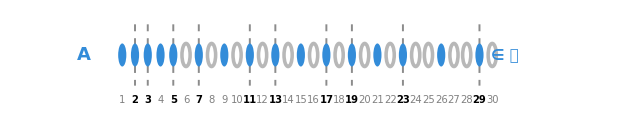
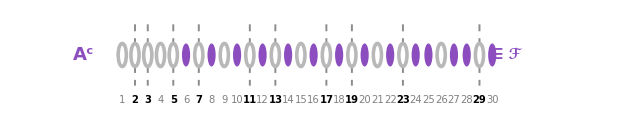
Un conjunto que contiene a todos los primos y su complementario, que no contiene ninguno
-Graphics-
-Graphics-complementario
-Graphics-

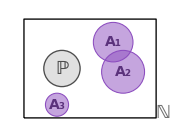
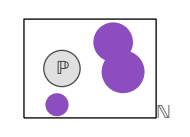
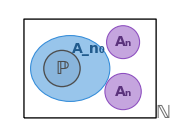
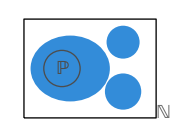
Cierre por uniones numerables: la unión de conjuntos de 𝒞 ∪ ℱ está en 𝒞 ∪ ℱ
Todos los conjuntos sin primos → la unión no tiene primos
-Graphics-
Cada A_n ∈ ℱ | -Graphics- | -Graphics-
∪ A_n ∈ ℱ
Algún conjunto contiene a todos los primos → la unión también
-Graphics-
A_n_0 ∈ 𝒞 | -Graphics- | -Graphics-
∪ A_n ∈ 𝒞

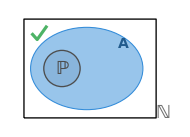
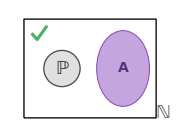
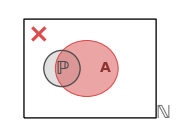
σ(𝒞) = 𝒞 ∪ ℱ: contiene a todos los primos o a ninguno
Contiene a todos los primos
-Graphics-
A ∈ 𝒞 | ∪ | No contiene ningún primo
-Graphics-
A ∈ ℱ |  | Contiene solo algunos primos
-Graphics-
A ∉ σ(𝒞)

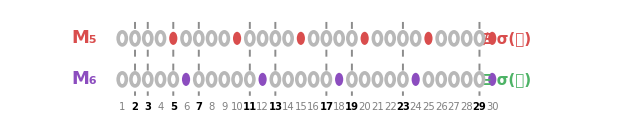
Múltiplos de 5 y de 6 frente a los números primos
-Graphics-
M_5 contiene al primo 5 pero no al 2, así que corta a ℙ.  M_6 no contiene ningún primo: M_6 ∈ ℱ ⊆ σ(𝒞)

```mathematica
diagramaPrimos1 = Column[{titulo1, panel1}, Alignment -> Center, Spacings -> 0.6]
diagramaPrimos2 = Column[{titulo2, panel2}, Alignment -> Center, Spacings -> 0.6]
diagramaPrimos3 = Column[{titulo3, panel3}, Alignment -> Center, Spacings -> 0.6]
diagramaPrimos4 = Column[{titulo4, panel4}, Alignment -> Center, Spacings -> 0.6]
```

```mathematica
Export[CloudObject["T1_P6_a.png"], diagramaPrimos1, "PNG", Background -> None, ImageResolution -> 300, ImageSize -> 700]
Export[CloudObject["T1_P6_b.png"], diagramaPrimos2, "PNG", Background -> None, ImageResolution -> 300, ImageSize -> 700]
Export[CloudObject["T1_P6_c.png"], diagramaPrimos3, "PNG", Background -> None, ImageResolution -> 300, ImageSize -> 700]
Export[CloudObject["T1_P6_d.png"], diagramaPrimos4, "PNG", Background -> None, ImageResolution -> 300, ImageSize -> 700]
```

CloudObject[https://www.wolframcloud.com/obj/jesusparejop/T1_P6_a.png]

CloudObject[https://www.wolframcloud.com/obj/jesusparejop/T1_P6_b.png]

CloudObject[https://www.wolframcloud.com/obj/jesusparejop/T1_P6_c.png]

CloudObject[https://www.wolframcloud.com/obj/jesusparejop/T1_P6_d.png]

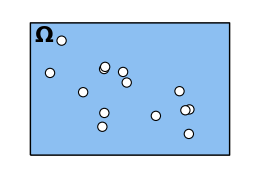
-Graphics-
A | complementario
-Graphics- | -Graphics-
Aᶜ
-Graphics-
A | complementario
-Graphics- | -Graphics-
Aᶜ

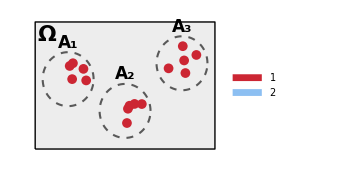
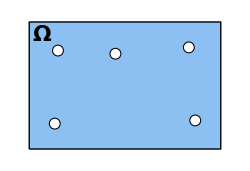
Caso 1 | -Graphics-
A_i numerables | ∪
-Graphics- | -Graphics-
∪ A_i
Caso 2 | -Graphics-
A_i₀ y los otros A_i | ∪
-Graphics- | -Graphics-
∪ A_i

```mathematica
ClearAll[colorNum, colorCo, puntos, etiquetaOmega, panelNum, panelCo, conEtq, flechaDoble, cuerpo, imagenFinal];

SeedRandom[11];
puntos = Table[{RandomReal[{0.5, 5.5}], RandomReal[{0.5, 3.5}]}, {14}];

colorNum = RGBColor[0.8, 0.15, 0.2];   (* numerable: puntos rojos *)
colorCo = RGBColor[0.55, 0.75, 0.95];  (* conumerable: región azul *)

etiquetaOmega = Text[Style["Ω", 22, Bold, Black], {0.4, 3.6}];

(* conjunto numerable: nube de puntos *)
panelNum = Graphics[{
    GrayLevel[0.93], EdgeForm[{Black, Thickness[0.004]}], Rectangle[{0, 0}, {6, 4}],
    colorNum, PointSize[0.03], Point[puntos],
    etiquetaOmega},
   PlotRange -> {{-0.2, 6.2}, {-0.2, 4.2}}, ImageSize -> 260];

(* conjunto conumerable: casi todo Omega, con agujeros en los puntos *)
panelCo = Graphics[{
    colorCo, EdgeForm[{Black, Thickness[0.004]}], Rectangle[{0, 0}, {6, 4}],
    White, EdgeForm[{Black, Thickness[0.003]}], Table[Disk[p, 0.14], {p, puntos}],
    etiquetaOmega},
   PlotRange -> {{-0.2, 6.2}, {-0.2, 4.2}}, ImageSize -> 260];

conEtq[g_, txt_] := Column[{g, Style[txt, 20, Bold]}, Alignment -> Center, Spacings -> 0.3];

flechaDoble = Column[{
    Style["complementario", 14, Italic],
    Graphics[{Black, AbsoluteThickness[3], Arrowheads[{{0.18, 0}, {0.18, 1}}],
      Arrow[{{0, 0}, {1, 0}}]},
     ImageSize -> {80, 35}, PlotRange -> {{-0.1, 1.1}, {-0.3, 0.3}}]},
   Alignment -> Center];

cuerpo = Grid[{
    {conEtq[panelNum, "A"], flechaDoble, conEtq[panelCo, "Aᶜ"]},
    {conEtq[panelCo, "A"], flechaDoble, conEtq[panelNum, "Aᶜ"]}},
   Alignment -> Center, Spacings -> {2, 2}];

T1P21a = Legended[cuerpo,
   SwatchLegend[{colorNum, colorCo}, {"conjunto numerable", "conjunto conumerable"},
    LabelStyle -> Directive[FontSize -> 16], LegendMarkerSize -> 20]];
T1P21a

ClearAll[colorNum, colorCo, etiquetaOmega, grupo, centros, grupos, base, panel, agujeros,
  huecos, cubiertos, descubiertos, extras, c1izq, c1der, c2izq, c2der, conEtq, flechaUnion,
  cuerpo, imagenFinal];

SeedRandom[5];

colorNum = RGBColor[0.8, 0.15, 0.2];
colorCo = RGBColor[0.55, 0.75, 0.95];

etiquetaOmega = Text[Style["Ω", 22, Bold, Black], {0.4, 3.6}];

(* nube de n puntos alrededor de un centro *)
grupo[c_, n_] := Table[
   Module[{t = RandomReal[{0, 2 Pi}], d = RandomReal[{0.1, 0.62}]}, c + d {Cos[t], Sin[t]}],
   {n}];

base[fondo_] := {fondo, EdgeForm[{Black, Thickness[0.004]}], Rectangle[{0, 0}, {6, 4}]};
panel[contenido_] := Graphics[{contenido, etiquetaOmega},
   PlotRange -> {{-0.2, 6.2}, {-0.2, 4.2}}, ImageSize -> 250];

(* ---------- Caso 1: todos los A_i numerables ---------- *)
centros = {{1.1, 2.2}, {3.0, 1.2}, {4.9, 2.7}};
grupos = Table[grupo[c, 5], {c, centros}];

c1izq = panel[{
    base[GrayLevel[0.93]],
    Table[{colorNum, PointSize[0.028], Point[grupos[[k]]]}, {k, 3}],
    Table[{GrayLevel[0.35], Dashed, AbsoluteThickness[1.5], Circle[centros[[k]], 0.85]}, {k, 3}],
    Table[Text[Style[Subscript["A", k], 17, Bold, Black], centros[[k]] + {0, 1.15}], {k, 3}]}];

c1der = panel[{base[GrayLevel[0.93]], colorNum, PointSize[0.028], Point[Flatten[grupos, 1]]}];

(* ---------- Caso 2: A_i0 conumerable ---------- *)
huecos = {{0.9, 3.1}, {1.8, 1.2}, {2.7, 3.0}, {3.4, 0.8}, {4.1, 2.2},
   {5.0, 3.2}, {5.2, 0.9}, {2.2, 2.1}, {0.8, 0.8}};   (* complemento de A_i0 *)
cubiertos = {2, 4, 5, 8};                              (* huecos que otros A_i vuelven a cubrir *)
descubiertos = Complement[Range[Length[huecos]], cubiertos];
extras = {{1.3, 2.2}, {3.3, 3.4}, {4.6, 1.6}, {5.4, 2.4}, {2.9, 1.7}};  (* otros puntos de los A_i *)

agujeros[lista_] := {White, EdgeForm[{Black, Thickness[0.003]}], Table[Disk[p, 0.17], {p, lista}]};

c2izq = panel[{
    base[colorCo],
    agujeros[huecos],
    colorNum, PointSize[0.028], Point[Join[huecos[[cubiertos]], extras]]}];

c2der = panel[{base[colorCo], agujeros[huecos[[descubiertos]]]}];

(* ---------- composición ---------- *)
conEtq[g_, txt_] := Column[{g, Style[txt, 20, Bold]}, Alignment -> Center, Spacings -> 0.3];

flechaUnion = Column[{
    Style["∪", 28, Bold],
    Graphics[{Black, AbsoluteThickness[3], Arrowheads[0.25], Arrow[{{0, 0}, {1, 0}}]},
     ImageSize -> {70, 30}, PlotRange -> {{-0.1, 1.1}, {-0.3, 0.3}}]},
   Alignment -> Center];

cuerpo = Grid[{
    {Style["Caso 1", 20, Bold],
     conEtq[c1izq, Row[{Subscript["A", "i"], " numerables"}]],
     flechaUnion,
     conEtq[c1der, Row[{"∪ ", Subscript["A", "i"]}]]},
    {Style["Caso 2", 20, Bold],
     conEtq[c2izq, Row[{Subscript["A", "i₀"], " y los otros ", Subscript["A", "i"]}]],
     flechaUnion,
     conEtq[c2der, Row[{"∪ ", Subscript["A", "i"]}]]}},
   Alignment -> Center, Spacings -> {2, 2}];

T1P21b = Legended[cuerpo,
   SwatchLegend[{colorNum, colorCo}, {"conjunto numerable", "conjunto conumerable"},
    LabelStyle -> Directive[FontSize -> 16], LegendMarkerSize -> 20]];
T1P21b
```

```mathematica
Export[CloudObject["T1_P21_a.png"],T1P21a, "PNG", Background -> None, ImageResolution -> 300, ImageSize -> 700]
Export[CloudObject["T1_P21_b.png"],T1P21b, "PNG", Background -> None, ImageResolution -> 300, ImageSize -> 700]
```

CloudObject[https://www.wolframcloud.com/obj/jesusparejop/T1_P21_a.png]

CloudObject[https://www.wolframcloud.com/obj/jesusparejop/T1_P21_b.png]

```mathematica
ClearAll[x, y, sepV, rV, limXV, limYV, enA, enB, atomCond, colAtom, miniAtoms, conEtq, sinEtq,
  etapa, flechaEtapa, etC, etC1, etC2, etC3, cuerpo, leyendaAtomos, imagenFinal];

sepV = 0.7; rV = 1.2; limXV = 2.7; limYV = 1.7;

enA = (x + sepV)^2 + y^2 < rV^2;
enB = (x - sepV)^2 + y^2 < rV^2;

(* las cuatro regiones del Venn: A∩Bᶜ, A∩B, Aᶜ∩B, Aᶜ∩Bᶜ *)
atomCond[1] = enA && ! enB;
atomCond[2] = enA && enB;
atomCond[3] = ! enA && enB;
atomCond[4] = ! enA && ! enB;

colAtom = {RGBColor[0.95, 0.6, 0.15], RGBColor[0.55, 0.3, 0.75],
   RGBColor[0.2, 0.55, 0.85], RGBColor[0.3, 0.7, 0.4]};

(* mini Venn que colorea las regiones indicadas en la lista inc *)
miniAtoms[inc_List, tam_: 105] := Show[
   Graphics[{GrayLevel[0.95], Rectangle[{-limXV, -limYV}, {limXV, limYV}]}],
   Sequence @@ Table[
     RegionPlot[Evaluate[atomCond[k]], {x, -limXV, limXV}, {y, -limYV, limYV},
      PlotStyle -> Directive[colAtom[[k]], Opacity[0.9]], BoundaryStyle -> None,
      PlotPoints -> 40, MaxRecursion -> 2],
     {k, inc}],
   Graphics[{FaceForm[None], EdgeForm[{Black, Thickness[0.007]}],
     Rectangle[{-limXV, -limYV}, {limXV, limYV}],
     Black, Thickness[0.007], Circle[{-sepV, 0}, rV], Circle[{sepV, 0}, rV]}],
   PlotRange -> {{-limXV, limXV}, {-limYV, limYV}}, AspectRatio -> Automatic, ImageSize -> tam];

conEtq[inc_List, txt_] := Column[{miniAtoms[inc], Style[txt, 16, Bold]},
   Alignment -> Center, Spacings -> 0.2];
sinEtq[inc_List] := miniAtoms[inc];

etapa[titulo_, iconos_List] := Column[{
    Style[titulo, 24, Bold],
    Column[iconos, Alignment -> Center, Spacings -> 0.8]},
   Alignment -> Center, Spacings -> 1];

flechaEtapa[txt_] := Column[{
    Style[txt, 14, Italic],
    Graphics[{Black, AbsoluteThickness[3], Arrowheads[0.25], Arrow[{{0, 0}, {1, 0}}]},
     ImageSize -> {70, 30}, PlotRange -> {{-0.1, 1.1}, {-0.3, 0.3}}]},
   Alignment -> Center];

etC = etapa["C", {conEtq[{1, 2}, "A"], conEtq[{2, 3}, "B"]}];

etC1 = etapa["C₁", {conEtq[{1, 2}, "A"], conEtq[{3, 4}, "Aᶜ"],
    conEtq[{2, 3}, "B"], conEtq[{1, 4}, "Bᶜ"]}];

etC2 = etapa["C₂", {sinEtq[{2}], sinEtq[{1}], sinEtq[{3}], sinEtq[{4}], sinEtq[{}]}];

etC3 = etapa["C₃ = 𝒬(C)",
   {sinEtq[{1, 2, 3}], sinEtq[{2, 4}], sinEtq[{1, 2, 3, 4}],
    Style["⋮", 24, Bold]}];

cuerpo = Grid[{{
    etC, flechaEtapa["complementos"], etC1, flechaEtapa["intersecciones"],
    etC2, flechaEtapa["uniones"], etC3}},
   Alignment -> {Center, Center}, Spacings -> {1.2, 0}];

leyendaAtomos = SwatchLegend[colAtom,
   {"A∩Bᶜ", "A∩B", "Aᶜ∩B", "Aᶜ∩Bᶜ"},
   LabelStyle -> Directive[FontSize -> 15], LegendMarkerSize -> 20];

T1P22a = Legended[cuerpo, leyendaAtomos];
T1P22a
ClearAll[x, y, sepV, rV, limXV, limYV, enA, enB, atomCond, colAtom, miniAtoms, conEtq, signo,
  flechaCorta, cuerpo, leyendaAtomos, imagenFinal];

sepV = 0.7; rV = 1.2; limXV = 2.7; limYV = 1.7;

enA = (x + sepV)^2 + y^2 < rV^2;
enB = (x - sepV)^2 + y^2 < rV^2;

atomCond[1] = enA && ! enB;
atomCond[2] = enA && enB;
atomCond[3] = ! enA && enB;
atomCond[4] = ! enA && ! enB;

colAtom = {RGBColor[0.95, 0.6, 0.15], RGBColor[0.55, 0.3, 0.75],
   RGBColor[0.2, 0.55, 0.85], RGBColor[0.3, 0.7, 0.4]};

miniAtoms[inc_List, tam_: 120] := Show[
   Graphics[{GrayLevel[0.95], Rectangle[{-limXV, -limYV}, {limXV, limYV}]}],
   Sequence @@ Table[
     RegionPlot[Evaluate[atomCond[k]], {x, -limXV, limXV}, {y, -limYV, limYV},
      PlotStyle -> Directive[colAtom[[k]], Opacity[0.9]], BoundaryStyle -> None,
      PlotPoints -> 40, MaxRecursion -> 2],
     {k, inc}],
   Graphics[{FaceForm[None], EdgeForm[{Black, Thickness[0.007]}],
     Rectangle[{-limXV, -limYV}, {limXV, limYV}],
     Black, Thickness[0.007], Circle[{-sepV, 0}, rV], Circle[{sepV, 0}, rV]}],
   PlotRange -> {{-limXV, limXV}, {-limYV, limYV}}, AspectRatio -> Automatic, ImageSize -> tam];

conEtq[inc_List, txt_] := Column[{miniAtoms[inc], Style[txt, 18, Bold]},
   Alignment -> Center, Spacings -> 0.2];

signo[txt_] := Style[txt, 30, Bold, GrayLevel[0.4]];

flechaCorta = Graphics[{Black, AbsoluteThickness[3], Arrowheads[0.25], Arrow[{{0, 0}, {1, 0}}]},
   ImageSize -> {60, 30}, PlotRange -> {{-0.1, 1.1}, {-0.3, 0.3}}];

(* fila 1: el complementario de una unión de piezas es la unión de las piezas restantes
   fila 2: la unión de dos elementos de C3 es otra unión de piezas *)
cuerpo = Grid[{
    {Style["Complementario", 18, Bold], conEtq[{2, 4}, "X"], flechaCorta,
     conEtq[{1, 3}, "Xᶜ"], "", "", ""},
    {Style["Unión", 18, Bold], conEtq[{1, 2}, "X"], signo["∪"],
     conEtq[{2, 3}, "Y"], signo["="], conEtq[{1, 2, 3}, "X∪Y"], ""}},
   Alignment -> {{Right, Center, Center, Center, Center, Center, Center}, Center},
   Spacings -> {1.5, 2}];

leyendaAtomos = SwatchLegend[colAtom,
   {"A∩Bᶜ", "A∩B", "Aᶜ∩B", "Aᶜ∩Bᶜ"},
   LabelStyle -> Directive[FontSize -> 15], LegendMarkerSize -> 20];

T1P22b = Legended[cuerpo, leyendaAtomos];
T1P22b
```

C
-Graphics-
A
-Graphics-
B | complementos
-Graphics- | C₁
-Graphics-
A
-Graphics-
Aᶜ
-Graphics-
B
-Graphics-
Bᶜ | intersecciones
-Graphics- | C₂
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics- | uniones
-Graphics- | C₃ = 𝒬(C)
-Graphics-
-Graphics-
-Graphics-
⋮

Complementario | -Graphics-
X | -Graphics- | -Graphics-
Xᶜ |  |  | 
Unión | -Graphics-
X | ∪ | -Graphics-
Y | = | -Graphics-
X∪Y |

```mathematica
Export[CloudObject["T1_P22_a.png"],T1P22a, "PNG", Background -> None, ImageResolution -> 300, ImageSize -> 700]
Export[CloudObject["T1_P22_b.png"],T1P22b, "PNG", Background -> None, ImageResolution -> 300, ImageSize -> 700]
```

CloudObject[https://www.wolframcloud.com/obj/jesusparejop/T1_P22_a.png]

CloudObject[https://www.wolframcloud.com/obj/jesusparejop/T1_P22_b.png]